Ultima atualização: 19/04/21 - 17h

```mathematica
(* Conferir:;
- Parametro K calculado com campo total no Erro de Fase;

Problemas:;
- ListShim criado com limite superior ao da criação da matriz de resposta

Adicionar:;


*)
```

## Load Radia

```mathematica
ClearAll["Global`*"]
<<Radia`;
RadPlot3DOptions[];
radUtiDelAll[]; (*Erase all previous elements*)
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

## Functions

### BlockGeometry

```mathematica
idBlockGeometry[checkgeo_]:=(
Module[{geo1,geo2,geo3},

(*Geo A1, Delta 52.5*)
If[checkgeo==1,
geo1={{-21.5,-50},{21.5,-50},{22.5,-49},{22.5,-41.8},{16.794,-37.654},{-16.794,-37.654},{-22.5,-41.8},{-22.5,-49}};
geo2={{16.794,-37.654},{16.794,-33.946},{-16.794,-33.946},{-16.794,-37.654}};
geo3={{16.794,-33.946},{22.5,-29.8},{22.5,-19.3},{5.25,0.0},{-5.25,0.0},{-22.5,-19.3},{-22.5,-29.8},{-16.794,-33.946}};
];

If[checkgeo==2,
geo1={{16.794,-37.654},{16.794,-33.946},{-16.794,-33.946},{-16.794,-37.654}};
geo2={{16.794,-33.946},{22.5,-29.8},{22.5,-19.3},{5.25,0.0},{-5.25,0.0},{-22.5,-19.3},{-22.5,-29.8},{-16.794,-33.946}};
];

Return[{geo1,geo2,geo3}]
];
)
```

### cassetteDraw

```mathematica
cassetteDraw::usage = "magnetizations = Lista das magnetizações dos blocos de um cassete (lista de tamanho n); blockGeo = {geo1,geo2,geo3}; 
termination = {{lista de magnetizacoes na entrada}, {lista de espessuras na entrada}, {lista de espaçamentos na entrada},{lista de magnetizacoes na saída}, {lista de espessuras na saída}, {lista de espaçamentos na saída}}"; 


idCassetteDraw[magnetizations_,blockGeo_,posErrors_,termination_,periodL_,blockThick_,gap_,blockGap_,subdiv_]:=(
Module[{cassette,block,obj,obj1,obj2,obj3,blocknumber,vacodym745ap,termLength,i,j,parts,randomErrorY,randomErrorZ,longPos},

cassette=radObjCnt[{}];
parts=Length[blockGeo];
obj=ConstantArray[{},parts];
blocknumber=Length[magnetizations]+Length[termination[[1]]]+Length[termination[[4]]];

(*Position Errors*)
If[posErrors[[1]]>0,
randomErrorY=Table[RandomVariate[NormalDistribution[posErrors[[1]]/2,(posErrors[[1]]/2)/3]],{i,1,blocknumber}]*RandomChoice[{-1,1},blocknumber];
,
randomErrorY=ConstantArray[0,blocknumber];
];
If[posErrors[[2]]>0,
randomErrorZ=Table[RandomVariate[NormalDistribution[posErrors[[2]]/2,(posErrors[[2]]/2)/3]],{i,1,blocknumber}]*RandomChoice[{-1,1},blocknumber];
,
randomErrorZ=ConstantArray[0,blocknumber];
];

(*===== Termination Front =====*)
block=ConstantArray[{},Length[termination[[1]]]];

For[i=1,i≤ Length[termination[[1]]],i++,
block[[i]]=radObjCnt[{}];

(*Next Block Position*)
If[i≤1,
longPos=0,
longPos=longPos+0.5*termination[[2,i-1]]+termination[[3,i-1]]+0.5*termination[[2,i]];
];

(*Create the Block Object*)
For[j=1,j≤ parts,j++,
(*Extrude part*)
obj[[j]]=radObjThckPgn[longPos,termination[[2,i]],blockGeo[[j]],termination[[1,i]]];
(*Part Subdivision*)
radObjDivMag[obj[[j]],subdiv[[j]]];
(*Add Part to block*)
radObjAddToCnt[block[[i]],{obj[[j]]}];
];

(*Position Error*)
radTrfOrnt[block[[i]],radTrfTrsl[{0,randomErrorY[[i]],randomErrorZ[[i]]}]];

(*Apply Material and Magnetization*)
vacodym745ap=radMatLin[{0.06,0.17},termination[[1,i]]];
radMatApl[block[[i]],vacodym745ap];

(*Add to Cassette*)
radObjAddToCnt[cassette,{block[[i]]}];
];

(*===== Periods =====*)
block=ConstantArray[{},Length[magnetizations]];

For[i=1,i≤ Length[magnetizations],i++,
block[[i]]=radObjCnt[{}];

(*Block Position*)
If[i≤1,
longPos=longPos+0.5*termination[[2,-1]]+termination[[3,-1]]+0.5*blockThick;
,
longPos=longPos+blockThick+blockGap;
];

For[j=1,j≤ parts,j++,
obj[[j]]=radObjThckPgn[longPos,blockThick,blockGeo[[j]],magnetizations[[i]]];
(*Part Subdivision*)
radObjDivMag[obj[[j]],subdiv[[j]]];
(*Add Part to block*)
radObjAddToCnt[block[[i]],{obj[[j]]}];
];

(*Position Error*)
radTrfOrnt[block[[i]],radTrfTrsl[{0,randomErrorY[[i]],randomErrorZ[[i]]}]];

(*Apply Material and Magnetization*)
vacodym745ap=radMatLin[{0.06,0.17},magnetizations[[i]]];
radMatApl[block[[i]],vacodym745ap]; 

(*Add to Cassette*)
radObjAddToCnt[cassette,{block[[i]]}];

];

(*===== Termination Back =====*)
block=ConstantArray[{},Length[termination[[1]]]];

For[i=1,i≤ Length[termination[[4]]],i++,
block[[i]]=radObjCnt[{}];

(*Next Block Position*)
If[i≤ 1,
longPos=longPos+blockThick/2+termination[[6,1]]+termination[[5,1]]/2;
,
longPos=longPos+0.5*termination[[5,i-1]]+termination[[6,i]]+0.5*termination[[5,i]];
];

For[j=1,j≤ parts,j++,
obj[[j]]=radObjThckPgn[longPos,termination[[5,i]],blockGeo[[j]],termination[[4,i]]];
(*Part Subdivision*)
radObjDivMag[obj[[j]],subdiv[[j]]];
(*Add Part to block*)
radObjAddToCnt[block[[i]],{obj[[j]]}];
];

(*Position Error*)
radTrfOrnt[block[[i]],radTrfTrsl[{0,randomErrorY[[i]],randomErrorZ[[i]]}]];

(*Apply Material and Magnetization*)
vacodym745ap=radMatLin[{0.06,0.17},termination[[4,i]]];
radMatApl[block[[i]],vacodym745ap]; 

(*Add to Cassette*)
radObjAddToCnt[cassette,{block[[i]]}];

];

Return[cassette]
];
)
```

### IDDraw

```mathematica
idDraw[typeID_,gap_,nPeriods_,periodL_,blockGeo_,blockThick_,blockGap_,magnetizations_,terminations_,mode_,subdiv_ ,posErrors_ :{0,0},gap2_ :0]:=(
Module[{device,cassette,mag,cassetteD,modeslist,phase,i,displacement,cassPos},
device=radObjCnt[{}];
cassette=ConstantArray[{},4];

(*==== Generate Cassettes =====*)
For[i=1,i≤Length[magnetizations],i++,
cassette[[i]]=idCassetteDraw[magnetizations[[i]],blockGeo,posErrors,terminations[[i]],periodL,blockThick,gap,blockGap,subdiv];

(*Apply Gap*)
radTrfOrnt[cassette[[i]],radTrfTrsl[{0,0,-gap/2}]];

If[typeID=="DeltaUndulator",
(*Apply Phase*)
(*modeslist={{0,0,0,0},{-1/4,0,-1/4,0},{-1/2,0,-1/2,0},{-1/4,0,1/4,0},{-1/4,-1/4,0,0},{-1/4,0,0,-1/4}}*periodL;*)
modeslist={{0,0,0,0},{1/4,0,1/4,0},{1/2,0,1/2,0},{1/4,0,-1/4,0},{-1/4,-1/4,0,0},{-1/4,0,0,-1/4}}*periodL;
phase=modeslist[[mode]];
radTrfOrnt[cassette[[i]],radTrfTrsl[{phase[[i]],0,0}]];

(*Apply Rotation*)
radTrfOrnt[cassette[[i]],radTrfRot[{0,0,0},{1,0,0},(i-1)*Pi/2]];
];

If[typeID=="PlanarUndulator",
(*Apply Phase*)
modeslist={{0,0},{0,-1/2},{0,-1/4},{0,1/2},{0,1/4}}*periodL;
phase=modeslist[[mode]];
radTrfOrnt[cassette[[i]],radTrfTrsl[{phase[[i]],0,0}]];

(*Apply Rotation*)
radTrfOrnt[cassette[[i]],radTrfRot[{0,0,0},{1,0,0},(i-1)*Pi]];
];

If[typeID=="EPU",
(*Apply Phase*)
modeslist={{0,0,0,0},{-1/4,0,-1/4,0},{-1/2,0,-1/2,0},{-1/4,0,1/4,0}}*periodL;
phase=modeslist[[mode]];
radTrfOrnt[cassette[[i]],radTrfTrsl[{phase[[i]],0,0}]];

(*Apply Position*)
zdesloc=gap+50/2; ydesloc=gap2+22; a=Min[Flatten[blockGeo,1][[All,2]]];
cassPos={{0,-ydesloc,0},{0,ydesloc,0},{0,ydesloc,2*zdesloc},{0,-ydesloc,2*zdesloc}};

radTrfOrnt[cassette[[i]],radTrfTrsl[cassPos[[i]]]];
];


radObjAddToCnt[device,{cassette[[i]]}];
];

If[typeID=="DeltaUndulator",
(*Rotate ID*)
radTrfOrnt[device,radTrfRot[{0,0,0},{1,0,0},-Pi/4]];
];

(*Adjust Axis*)
device=radTrfOrnt[device,radTrfRot[{0,0,0},{0,1,0},-Pi/2]];
device=radTrfOrnt[device,radTrfRot[{0,0,0},{0,0,1},-Pi/2]];
(*Ficou faltando rotacionar 180° em Z*)
(*radTrfOrnt[device,radTrfRot[{0,0,0},{0,0,1},3*Pi/2]];*)

Return[device];
];
)
```

### Generate Block Mag

```mathematica
idGenerateMag[typeID_,nPeriods_,periodL_,blockThick_,blockGap_,symmetry_,magnAmp_,magError_ :0,magAmpError_ :0.02,magTheta_ :1]:=(
Module[{mag,magnetization,j,i,termination,phi,theta,dmag},

(*===== ID Type =====*)
If[typeID=="DeltaUndulator",
mag={{{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}},{{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}}};
];

If[typeID=="PlanarUndulator",
mag={{{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}}};
];

If[typeID=="EPU",
mag={{{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}},{{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}},{{magnAmp,0,0},{0,0,-magnAmp},{-magnAmp,0,0},{0,0,magnAmp}},{{magnAmp,0,0},{0,0,-magnAmp},{-magnAmp,0,0},{0,0,magnAmp}}};
];

(*===== Create Cassette Magnetizations =====*)
magnetization=ConstantArray[{},Length[mag]];

For[j=1,j≤ Length[mag],j++,
magnetization[[j]]=Nest[Join[mag[[j]],#,1]&,mag[[j]],(nPeriods-1)];
If[symmetry=="symmetric",
magnetization[[j]]=Delete[magnetization[[j]],-1];
,
magnetization[[j]]=Join[magnetization[[j]],{magnetization[[j,1]]}];
];
];

(*===== Generate Errors =====*)
phi=RandomReal[{0,2*Pi},Length[Flatten[magnetization,1]]];
phi=ArrayReshape[phi,{Length[magnetization],Length[magnetization[[1]]]}];

theta=Table[RandomVariate[NormalDistribution[0,(magTheta*Pi/180)/3]],{i,1,Length[Flatten[magnetization,1]]}];
theta=ArrayReshape[theta,{Length[magnetization],Length[magnetization[[1]]]}]; 

If[magError≥1,
dmag=1+Table[RandomVariate[NormalDistribution[0,magAmpError/3]],{i,1,Length[Flatten[magnetization,1]]}];
dmag=ArrayReshape[dmag,{Length[magnetization],Length[magnetization[[1]]]}]; 
,
dmag=ConstantArray[1,{Length[magnetization],Length[magnetization[[1]]]}];
phi=phi*0;
theta=theta*0;
];

(*===== Apply Errors =====*)
For[i=1,i≤ Length[magnetization],i++,
magnetization[[i]]=magnetization[[i]]*dmag[[i]];

For[j=1,j≤ Length[magnetization[[1]]],j++,
If[Mod[j,2]≤0,
magnetization[[i,j]]=RotationMatrix[phi[[i,j]],{0,0,1}].RotationMatrix[theta[[i,j]],{0,1,0}].magnetization[[i,j]];
,
magnetization[[i,j]]=RotationMatrix[phi[[i,j]],{1,0,0}].RotationMatrix[theta[[i,j]],{0,1,0}].magnetization[[i,j]];
];
]

];
Return[magnetization]
];
)
```

### GenerateTermination Mag

```mathematica
idGenerateTerm[termType_,blockThick_,blockGap_,periodL_,magnAmp_,magFront_ :{{}},magBack_ :{{}},magError_ :0,magAmpError_ :0.01,magTheta_ :1]:=(
Module[{termination,termMagFront,termMagBack,termBlockThick,termBlockGap,dmag,phi,theta,size},
(*----- ThreeBlocksAntiSym Termination -----*)
If[termType=="ThreeBlocksAntiSym",
If[Length[magFront[[1]]]≥ 3,
termMagFront=magFront;
,
termMagFront={{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}},{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}}};
];

If[Length[magBack[[1]]]≥ 3,
termMagBack=magBack;
,
termMagBack={{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}},{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}}};
];

termBlockThick={1/4,1/2,3/4}*blockThick;
termBlockGap={0.875*periodL/4-((0.25+0.5)/2*blockThick),0.875*periodL/4-((0.5+0.75)/2*blockThick),0.875*periodL/4-((0.75+1)/2*blockThick)};

termination=Table[{termMagFront[[i]],termBlockThick,termBlockGap,termMagBack[[i]],Reverse[termBlockThick],Reverse[termBlockGap]},{i,1,Length[termMagFront]}];
];
(*-------------------------------------------------------------*)
(*----- FourBlocksAntiSym Termination -----*)
If[termType=="FourBlocksAntiSym",
If[Length[magFront[[1]]]≥ 4,
termMagFront=magFront;
,
termMagFront={{{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}},{{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}}};

(*Apply Errors*)
If[magError≥1,
size=Dimensions[termMagFront];
dmag=1+Table[RandomVariate[NormalDistribution[0,magAmpError/3]],{i,1,Length[Flatten[termMagFront,1]]}];
termMagFront=Flatten[termMagFront,1]*dmag;

phi=RandomReal[{0,2*Pi},Length[termMagFront]];
theta=Table[RandomVariate[NormalDistribution[0,(magTheta*Pi/180)/3]],{i,1,Length[termMagFront]}];

For[i=1,i≤ Length[termMagFront],i++,
If[Mod[i,2]≤0,
termMagFront[[i]]=RotationMatrix[phi[[i]],{0,0,1}].RotationMatrix[theta[[i]],{0,1,0}].termMagFront[[i]];
,
termMagFront[[i]]=RotationMatrix[phi[[i]],{1,0,0}].RotationMatrix[theta[[i]],{0,1,0}].termMagFront[[i]];
]];
termMagFront=ArrayReshape[termMagFront,size];
]
];

If[Length[magBack[[1]]]≥ 4,
termMagBack=magBack;
,
termMagBack={{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0}},{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0}},{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0}},{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0}}};

(*Apply Errors*)
If[magError≥1,
size=Dimensions[termMagBack];
dmag=1+Table[RandomVariate[NormalDistribution[0,magAmpError/3]],{i,1,Length[Flatten[termMagBack,1]]}];
termMagBack=Flatten[termMagBack,1]*dmag;

phi=RandomReal[{0,2*Pi},Length[termMagBack]];
theta=Table[RandomVariate[NormalDistribution[0,(magTheta*Pi/180)/3]],{i,1,Length[termMagBack]}];

For[i=1,i≤ Length[termMagBack],i++,
If[Mod[i,2]>0,
termMagBack[[i]]=RotationMatrix[phi[[i]],{0,0,1}].RotationMatrix[theta[[i]],{0,1,0}].termMagBack[[i]];
,
termMagBack[[i]]=RotationMatrix[phi[[i]],{1,0,0}].RotationMatrix[theta[[i]],{0,1,0}].termMagBack[[i]];
]];
termMagBack=ArrayReshape[termMagBack,size];
]
];

termBlockThick={3.25,3.25,9.75,9.75};
termBlockGap={8.7,2.0,3.3,1.0};

termination=Table[{termMagFront[[i]],termBlockThick,termBlockGap,termMagBack[[i]],Reverse[termBlockThick],Reverse[termBlockGap]},{i,1,Length[termMagFront]}];
];
(*-------------------------------------------------------------*)

Return[termination]
];
)
```

### Solve

```mathematica
idSolve[device_,randomization_ :{1*^-10,1*^-10,1*^-10}]:=(
Module[{abs,rel,zero,re,t0,t1},
t0=AbsoluteTime[];

radFldLenTol[randomization[[1]],randomization[[2]],randomization[[3]]];

re=RadSolve[device,1*^-10,100000];
(*t1=AbsoluteTime[];
Print["> Insertion Device solved: (Elapsed Time: ",t1-t0,"[s])"]*)
]
)
```

### Field Calc

```mathematica
idField[undulator_,li_,lf_,lNpts_,{posV_,posH_},display_,oneplot_]:=(
Module[{lstep,t0,t1,baxis,btotal,axispoints,plot},
lstep=(lf-li)/lNpts;
t0=AbsoluteTime[];

(*----- Axis Field Calc -----*)
baxis=Table[radFld[undulator,"b",{posH,posV,z}],{z,li,lf-lstep,lstep}];

t1=AbsoluteTime[];
(*Print["> Field Components: (elapsed time: ",t1-t0 ,"[s])"];*)

(*----- Plots -----*)
If[display≥ 1,
plot=ConstantArray[{},3];
(*Axis Plot*)
axispoints=Table[li+(n-1)*lstep,{n,1,lNpts}];
plot[[1]]=ListLinePlot[Table[{axispoints[[i]],baxis[[i,1]]},{i,1,lNpts}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["Magnetic Field [T]",12]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,PlotLegends->Placed[{"Bx"},Above]];
plot[[2]]=ListLinePlot[Table[{axispoints[[i]],baxis[[i,2]]},{i,1,lNpts}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["Magnetic Field [T]",12]},PlotTheme->"Detailed",PlotStyle->{Orange},ImageSize->Medium,PlotRange->All,PlotLegends->Placed[{"By"},Above]];
plot[[3]]=ListLinePlot[Table[{axispoints[[i]],baxis[[i,3]]},{i,1,lNpts}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["Magnetic Field [T]",12]},PlotTheme->"Detailed",PlotStyle->{Green},ImageSize->Medium,PlotRange->All,PlotLegends->Placed[{"Bz"},Above]];

If[oneplot≥1,
maxims=Table[{i,Max[baxis[[All,i]]]},{i,1,3}];
plotOrder=SortBy[maxims,Last];
Print[Show[Table[plot[[plotOrder[[-i,1]]]],{i,1,3}]]];
,
Print[GraphicsRow[{plot[[1]],plot[[2]],plot[[3]]},Spacings->{0,10},ImageSize->{1200,300},AspectRatio->Full]];
];
];

Return[baxis]
];
)
```

### Field Integral

```mathematica
idFieldInt[undulator_,li_,lf_,lstep_,baxis_,display_,oneplot_]:=(
Module[{i,dz,area,area2,integral,integral2,firstInt,secondInt,axispoints,plot,t0,t1},
(*----- First Integral -----*)
t0=AbsoluteTime[];
dz=lstep;

area=Table[{(baxis[[i,1]]+baxis[[i+1,1]])/2*dz,(baxis[[i,2]]+baxis[[i+1,2]])/2*dz,(baxis[[i,3]]+baxis[[i+1,3]])/2*dz},{i,1,Length[baxis]-1}];
integral=Accumulate[area]; (*T.mm*)
firstInt=integral*10^4/10 ;(*G.cm*)

(*----- Second Integral -----*)
area2=Table[{(integral[[i,1]]+integral[[i+1,1]])/2*dz,(integral[[i,2]]+integral[[i+1,2]])/2*dz,(integral[[i,3]]+integral[[i+1,3]])/2*dz},{i,1,Length[integral]-1}];
integral2=Accumulate[area2];(*T.mm.b2*)
secondInt=(integral2*10^4/100)/1000; (*kG.cm.b2*)

t1=AbsoluteTime[];

(*Print["> Field Integrals: elapsed time = ",(t1-t0)," [s]"];*)

(*Print["First integrals : ", firstInt[[-1]]," [G.cm]"];
Print["Second integrals : ", secondInt[[-1]]," [kG.cm.b2]"];*)

(*----- Plots -----*)
If[display≥ 1,
plot=ConstantArray[{},3];
axispoints=Table[(li+lstep/2)+(n-1)*lstep,{n,1,Length[baxis]-1}];

plot[[1]]=ListLinePlot[Table[{axispoints[[i]],firstInt[[i,1]]},{i,1,Length[firstInt]}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["Field Integral [G.cm]",12]},PlotTheme->"Detailed",ImageSize->Medium,PlotLegends->Placed[{"Bx"},Above]];
plot[[2]]=ListLinePlot[Table[{axispoints[[i]],firstInt[[i,2]]},{i,1,Length[firstInt]}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["Field integral [G.cm]",12]},PlotTheme->"Detailed",PlotStyle->{Orange},ImageSize->Medium,PlotLegends->Placed[{"By"},Above]];
plot[[3]]=ListLinePlot[Table[{axispoints[[i]],firstInt[[i,3]]},{i,1,Length[firstInt]}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["Field integral [G.cm]",12]},PlotTheme->"Detailed",PlotStyle->{Green},ImageSize->Medium,PlotLegends->Placed[{"Bz"},Above]];

If[oneplot≥1,
maxims=Table[{i,Max[firstInt[[All,i]]]},{i,1,3}];
plotOrder=SortBy[maxims,Last];
Print[Show[Table[plot[[plotOrder[[-i,1]]]],{i,1,3}]]];
,
Print[GraphicsRow[plot,Spacings->{0,10},ImageSize->{1200,300},AspectRatio->Full]];
];
];

Return[{firstInt,secondInt}]
];
)
```

### Trajectory - RungeKutta4

```mathematica
idTrajectory::usage = "IDRungeKuttaTrajectory[device, energy, r0, smax, rkstep]: Calculates the particle trajectory using the Runge-Kutta algorithm. The particle energy must be in GeV, r0 is the initial position and normalized momentum vector {x0, y0, z0, dx0ds, dy0ds, dz0ds}, smax and rkstep are the final longitudinal position and the Runge-Kutta step. All positions are in millimeters.";

idTrajectory[device_, energy_,r0_,smax_,rkstep_,display_] := Module[
{trajectory, ElectronRestEnergy, LightSpeed, beta, brho, a, b, b1, b2, b3, r,rp, r1, r2, r3, drds1, drds2, drds3, drds4, i, sm, step, t0, t1,p1,p2},

t0=AbsoluteTime[];

ElectronRestEnergy=510998.92811; (*[eV]*)
LightSpeed=299792458;(*[m/s]*)

beta=Sqrt[1.0-(1.0/((energy*1000000000/ElectronRestEnergy)^2))];
brho=(beta*energy*1000000000/LightSpeed);
a=1.0/brho;

r1 = {0,0,0,0,0,0};
r2 = {0,0,0,0,0,0};
r3 = {0,0,0,0,0,0};
r= r0;

(*from mm to m*)
r[[1]]= r[[1]]/1000; r[[2]]= r[[2]]/1000; r[[3]]= r[[3]]/1000;
sm = smax/1000;
step = rkstep/1000;

trajectory={};
AppendTo[trajectory, {r[[1]]*1000, r[[2]]*1000, r[[3]]*1000, r[[4]], r[[5]], r[[6]]}];

While [r[[3]]<sm,
rp =r;
b=radFld[device, "BxByBz", 1000*rp[[;;3]]];
	drds1=auxIDNewtonLorentzEquation[a,r,b];
r1=rp+(step/2.0)*drds1;

b1=radFld[device, "BxByBz", 1000*r1[[;;3]]];
	drds2=auxIDNewtonLorentzEquation[a,r1,b1];
r2=rp+(step/2.0)*drds2;

b2=radFld[device, "BxByBz", 1000*r2[[;;3]]];
drds3=auxIDNewtonLorentzEquation[a,r2,b2];
r3=rp+step*drds3;

b3=radFld[device, "BxByBz", 1000*r3[[;;3]]];
drds4=auxIDNewtonLorentzEquation[a,r3,b3];
r=rp+(step/6.0)*(drds1+2.0*drds2+2.0*drds3+drds4);

AppendTo[trajectory, {r[[1]]*1000, r[[2]]*1000, r[[3]]*1000, r[[4]], r[[5]], r[[6]]}];
];

t1=AbsoluteTime[];
(*Print["> IDRungeKuttaTrajectory: elapsed time = ",(t1-t0)," s"];*)

If[display≥ 1,
(*Plots*)
p1=ListLinePlot[Table[{trajectory[[i,3]],trajectory[[i,1]]},{i,1,Length[trajectory]}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["X [mm]",12]},PlotLabel->Style["X Direction Trajectory",Bold,12],PlotTheme->"Detailed",ImageSize->Medium];
p2=ListLinePlot[Table[{trajectory[[i,3]],trajectory[[i,2]]},{i,1,Length[trajectory]}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["Y [mm]",12]},PlotLabel->Style["Y Direction Trajectory",Bold,12],PlotTheme->"Detailed",ImageSize->Medium];

Print[Row[{p1,p2},"\t\t"]];
];

Return[trajectory];
];
```

### AuxRungeKutta

```mathematica
auxIDNewtonLorentzEquation[a_,r_,b_]:=Module[
{drds},
drds = {0,0,0,0,0,0};
drds[[1]]=r[[4]];
drds[[2]]=r[[5]];
drds[[3]]=r[[6]];
drds[[4]]=-a*(r[[5]]*b[[3]]-r[[6]]*b[[2]]);
drds[[5]]=-a*(r[[6]]*b[[1]]-r[[4]]*b[[3]]);
drds[[6]]=-a*(r[[4]]*b[[2]]-r[[5]]*b[[1]]);
Return[drds];
];
```

### PhaseError - RungeKutta

```mathematica
idPhaseError[baxis_,xo_,xf_,nx_,Trajetoria_,eEnergy_]:=(
Module[{eletron,mo,eRestEnergy,bfield,bfieldT,longAxis,ampX,ampY,ampZ,ampT,peakX,peakY,peakZ,peakT,longPeak,longPeakX,longPeakY,longPeakZ,longPeakT,periods,nperiods,periodL,kparam,gamma,lambda,intField0,intField,drop,phaseError,phase,j,jmin,rmsError,fitData,fitLin,linearFit,linearizedPhase,p3,a,b,I00,I0,p0,btotal,dx,c,s,errorP,t0,t1},
t0=AbsoluteTime[];

(*Check Inputs*)
If[Length[baxis≠ Length[Trajetoria]],Return["[ERROR] : Field vector and Trajectory Vector have not the same lenght."]];
If[eEnergy>100,Return["[ERROR] : Electron beam energy to high. Check if the input energy is in Gev."]];

(*Total Field*)
btotal=Sqrt[baxis[[All,1]]^2+baxis[[All,2]]^2+baxis[[All,3]]^2];

(*===== Parameters =====*)
eletron=1.60217662*^-19; mo=9.10938356*^-31;
eRestEnergy=510998.92811; (*[eV]*) (* == mo*c^2[J]*)
c=299792458; (*m/s*)

bfield=baxis;
bfieldT=btotal;

(*Principal Longitudinal Axis*)
dx=(xf-xo)/nx;
longAxis=Table[xo+(n-1)*dx,{n,1,nx}];

(* Longitudinal Axis from 0 *)
s=(longAxis-longAxis[[1]])/1000;  (*[m]*)

(*===== Find Peaks =====*)
ampT=0.1*Max[bfieldT];
ampX=ampY=ampZ=ampT;
(*Find Peaks*)
peakX=FindPeaks[bfield[[All,1]],0 ,0, ampX];
peakY=FindPeaks[bfield[[All,2]],0 ,0, ampY];
peakZ=FindPeaks[bfield[[All,3]],0 ,0, ampZ];
peakT=FindPeaks[bfieldT,0 ,0 , ampT];

(*===== Remove extremities from Total Field =====*)
drop=4; (*how many peaks to drop each side*)
peakT=Drop[peakT,{1,drop}];peakT=Drop[peakT,{-drop,-1}]; (*Drop extremity peaks*)
longPeakT=Table[s[[peakT[[i,1]]]],{i,1,Length[peakT]}]; (*Crate longitudinal axis based on total field*)

(*===== Remove extremities from Field Components =====*)
drop=3; (*how many peaks to drop each side*)
(*Z axis*)
If[Length[peakZ]>2*drop,
peakZ=Drop[peakZ,{1,drop}];peakZ=Drop[peakZ,{-drop,-1}];
longPeakZ=Table[longAxis[[peakZ[[i,1]]]],{i,1,Length[peakZ]}];
,
peakZ=ConstantArray[10^-5,{1,2}];
];
(*Y axis*)
If[Length[peakY]>2*drop,
peakY=Drop[peakY,{1,drop}];peakY=Drop[peakY,{-drop,-1}];
longPeakY=Table[longAxis[[peakY[[i,1]]]],{i,1,Length[peakY]}];
,
peakY=ConstantArray[10^-5,{1,2}];
];
(*X axis*)
If[Length[peakX]>2*drop,
peakX=Drop[peakX,{1,drop}];peakX=Drop[peakX,{-drop,-1}];
longPeakX=Table[longAxis[[peakX[[i,1]]]],{i,1,Length[peakX]}];
,
peakX=ConstantArray[10^-5,{1,2}];
];

(*===== Find the Principal Field Axis =====*)
If[Mean[peakX[[All,2]]]>Mean[peakY[[All,2]]],
If[Mean[peakX[[All,2]]]>Mean[peakZ[[All,2]]],
longPeak=longPeakX;
,
longPeak=longPeakZ;
]
,
If[Mean[peakY[[All,2]]]>Mean[peakZ[[All,2]]],
longPeak=longPeakY;
,
longPeak=longPeakZ;
]
];

periods=Table[longPeak[[i+1]]-longPeak[[i]],{i,1,Length[longPeak]-1}];

(*========= Magnet design =========*)
nperiods=Length[periods];
periodL=Mean[periods]; (*mm*)
gamma=eEnergy*10^9/eRestEnergy;
kparam=0.0934*periodL*Mean[peakT[[All,2]]];  (*!!!!!!!!!!!!! Todas componentes ou só 1? *)
lambda=((Mean[periods]/1000)/(2*(gamma^2)))*(1 + (kparam^2)/2); (*m*)

(*========= Phase Function =========*)
jmin=peakT[[1,1]];
phase={};

I0=Table[(((Trajetoria[[i,4]]^2+Trajetoria[[i+1,4]]^2)/2)+((Trajetoria[[i,5]]^2+Trajetoria[[i+1,5]]^2)/2))*(s[[i+1]]-s[[i]]),{i,1,jmin}];
p0=Pi/lambda*(s[[jmin]]/gamma^2+Sum[I0[[i]],{i,1,Length[I0]}]);
AppendTo[phase,p0];

For[j=jmin+1,j≤(peakT[[Length[peakT],1]]-2),j++,

I00=(((Trajetoria[[j,4]]^2+Trajetoria[[j+1,4]]^2)/2)+((Trajetoria[[j,5]]^2+Trajetoria[[j+1,5]]^2)/2))*(s[[j+1]]-s[[j]]);
AppendTo[I0,I00];
p0=Pi/lambda*(s[[j]]/gamma^2+Sum[I0[[i]],{i,1,Length[I0]}]);

AppendTo[phase,p0];
];

(*========= Fitting ========= *)
fitData=Table[{s[[i]]+longPeakT[[1]],phase[[i]]},{i,1,Length[phase]}];
fitLin=NonlinearModelFit[fitData,a*x+b,{a,b},x];

linearFit=Table[{s[[i]]+longPeakT[[1]],fitLin[s[[i]]+longPeakT[[1]]]},{i,1,Length[phase]}];
linearizedPhase=phase-linearFit[[All,2]];

p3=ListLinePlot[linearizedPhase*180/Pi,PlotLabel->"Linearized Phase",ImageSize->{300,200},Frame->True,FrameLabel->{" ","[deg]"}];

errorP=Table[Mean[linearizedPhase[[peakT[[i,1]]-peakT[[1,1]]+1;;peakT[[i+1,1]]-peakT[[1,1]]-1]]],{i,1,Length[peakT]-1}]*180/Pi;

t1=AbsoluteTime[];
(*Print["> Phase solved: elapsed time = ",t1-t0,"[s]"];*)

Return[errorP]
];
)
```

### BlocksPosition

```mathematica
idBlocksPosition[magnetizations_,terminations_,blockThick_,blockGap_]:=(
Module[{longPos,nTotalBl,nCasseteBl,blockidx},

nTotalBl=(Length[magnetizations[[1]]]+Length[terminations[[1,1]]]+Length[terminations[[1,4]]])*4;
nCasseteBl=nTotalBl/4;

longPos=ConstantArray[0,nCasseteBl]; 
blockidx=1;

For[i=2,i≤ Length[terminations[[1,1]]],i++,
longPos[[i]]=longPos[[i-1]]+0.5*terminations[[1,2,i-1]]+terminations[[1,3,i-1]]+0.5*terminations[[1,2,i]];
blockidx+=1;
];

	blockidx+=1;longPos[[blockidx]]=longPos[[blockidx-1]]+0.5*terminations[[1,2,-1]]+terminations[[1,3,-1]]+0.5*blockThick;

	For[i=2,i≤ Length[magnetizations[[1]]],i++,
blockidx+=1;
longPos[[blockidx]]=longPos[[blockidx-1]]+blockThick+blockGap;
];

	blockidx+=1;
longPos[[blockidx]]=longPos[[blockidx-1]]+blockThick/2+terminations[[1,6,1]]+terminations[[1,5,1]]/2;

For[i=2,i≤ Length[terminations[[1,4]]],i++,
blockidx+=1;
longPos[[blockidx]]=longPos[[blockidx-1]]+0.5*terminations[[1,5,i-1]]+terminations[[1,6,i]]+0.5*terminations[[1,5,i]];
];

Return[longPos]
];
)
```

## Calculo

### Parameters

```mathematica
(*===== Magnetic Design =====*)
periodL=52.5; (*Period Length [mm]*)
gap=13.6; (*Minimum ID gap [mm]*)
nPeriods=21; (*number of periods without terminations*)
blockGap=0.125; (*space between blocks [mm]*)
eEnergy = 3; (*Particle energy [GeV]*)

(*==== Magnetic Blocks =====*)
blockGeo=idBlockGeometry[1]; (*Blocks Geometry: 1=A1*)
blockThick=13; (*Block Thickness [mm]*)
magInput=2; (*Type of input for Magnetizations: [1]Import from File ; [2]Aleatory Generation*)

fileNameB="Magnetizations.xlsx"; (*Magnetizations File name (with extension)*)
headLineB=0; (*Number of Head Lines on the File*)
fileNameT="Magnetizations_Term.xlsx"; (*Magnetizations File name (with extension)*)
headLineT=0; (*Number of Head Lines on the File*)

magnAmp=1.37; (*Remanent Block Magnetization [T]*)
magError=1; (*Include(1) or not(0) magnetization errors*)
magAmpError=0.01*magnAmp; (*Magnetization Amplitude Error [T]*)
magTheta=1; (*Magnetization Angle Error [deg]*)
posErrors={0,0}; (*Position Error Limit {x,y}+-[mm] *)

(*===== Other Parameters =====*)
mode=1; (*Phase: 1=Linear Hor. | 2=?*)
symmetry="antisymmetric"; (*ID symmetry: "symmetric" or "antisymmetric"*)
termType="FourBlocksAntiSym"; (*Termination Type: "ThreeBlocksAntiSym" | "ThreeBlocksAntiSymReal" | "ThreeBlockSym" | ?"Simple-Half"? *)
typeID="DeltaUndulator"; (*"DeltaUndulator" | "PlanarUndulator" | "EPU"*)
gap2=0; (*Horizontal gap in case of EPU undulator [mm]*)

(*===== Calculation Parameters =====*)
subdiv={{2,1,1},{1,1,1},{1,2,2}}; (*subdivisons on each part of the block geometry, for each direction (nx,ny,nz): {{nx,ny,nz},{nx,ny,nz},{nx,ny,nz}}*)

(*Longitudinal Range [mm]*)
lstep =1; (*Longitudinal Step [mm]*)
oversize=200; (*Excess on each side to start and finish the computations [mm]*)
li = -oversize;
lf =(nPeriods+2)*periodL+oversize;
lNpts =Round[(lf -li)/lstep ]+ 1; 

(*===== Sorting Parameters =====*)
nphase=3; (*number of phases to consider on Otimization: {LinearHoriz, LinearCirc, LinearVert}*)
genNumber=1; (*number of Generations*)
genSize=10; (*size of each generation from 2nd*)
firstGenSize=50; (*size of the 1st generation*)
```

### Import Data

#### Magnetizations

```mathematica
dir=NotebookDirectory[];

DumpGet[StringJoin[dir,"magnetizations2.mx"]];
magnetizations=magnetizations2;
DumpGet[StringJoin[dir,"terminations2.mx"]];
terminations=terminations2;
```

#### Response Matrix

```mathematica
(*M=Import[StringJoin[dir,"Response_Matrix_Tbl.txt"],"Table"];*)
DumpGet[StringJoin[dir,"responseMatrix.mx"]];

(*Invert Matrix*)
Minv=PseudoInverse[responseMatrix];
```

#### Matrix analysis

```mathematica
{u,w,v}=SingularValueDecomposition[responseMatrix];
```

```mathematica
Print["Matrix U: ",Dimensions[u][[1]]," x ",Dimensions[u][[2]],
"\nMatrix W: ",Dimensions[w][[1]]," x ",Dimensions[w][[2]],
"\nMatrix V: ",Dimensions[v][[1]]," x ",Dimensions[v][[2]]]
```

Matrix U: 4827 x 4827
Matrix W: 4827 x 372
Matrix V: 372 x 372

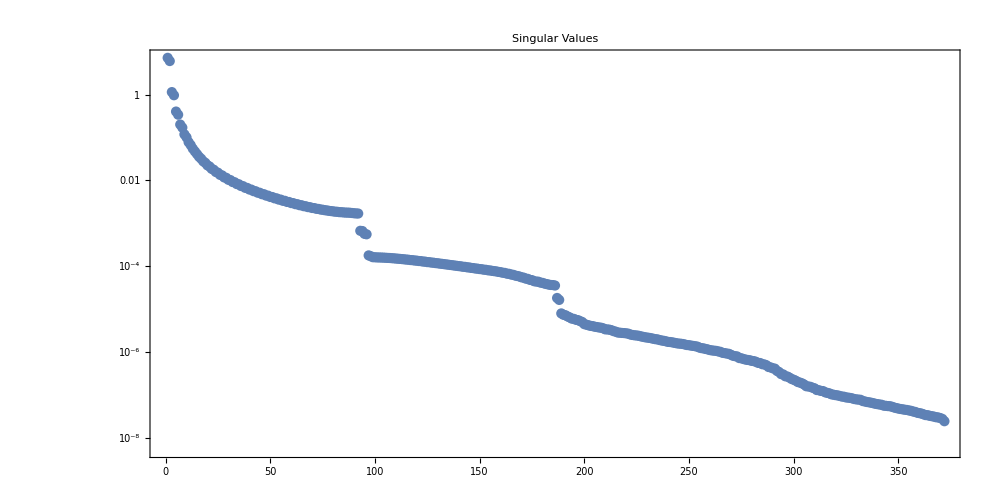

```mathematica
singValues=Table[w[[i,i]],{i,1,Min[Dimensions[w]]}];
ListLogPlot[singValues,PlotTheme->"Detailed",PlotRange->All,AspectRatio->1/2,ImageSize->{1000,300},PlotLabel->Style["Singular Values",14,Bold]]
```

```mathematica
DumpGet[StringJoin[dir,"listShim.mx"]];
```

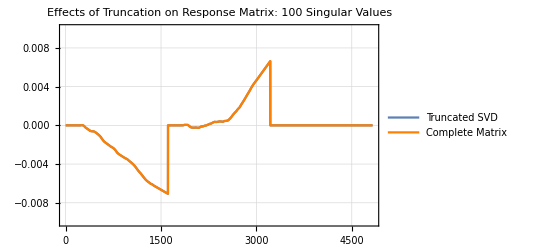

```mathematica
(*truncation=10^0;
rank=Count[singValues,x_/;x≥ truncation];*)
rank=100;

(*Matrix Dimension Adjust*)
wt=w[[1;;Dimensions[w][[2]],All]];
winv=wt;
For[i=1,i=Length[winv],i++,winv[[i,i]]=1/winv[[i,i]]];
ut=u[[All,1;;Dimensions[w][[2]]]];

(*Truncating singular values*)
For[i=rank+1,i≤Length[wt],i++,wt[[i,i]]=0];
For[i=rank+1,i≤Length[winv],i++,winv[[i,i]]=0];

Xr=ut.wt.Transpose[v];

(*Compare Matrix Responses*)
R1=responseMatrix.listShim;
R2=Xr.listShim;

Show[{ListLinePlot[R2,PlotTheme->"Detailed",PlotLegends->{"Truncated SVD"},PlotRange->{All,{-0.01,0.01}},PlotLabel->Style[StringJoin["Effects of Truncation on Response Matrix: ",ToString[rank]," Singular Values"],Bold]],ListLinePlot[R1,PlotTheme->"Detailed",PlotStyle->Orange,PlotLegends->{"Complete Matrix"}]}]
```

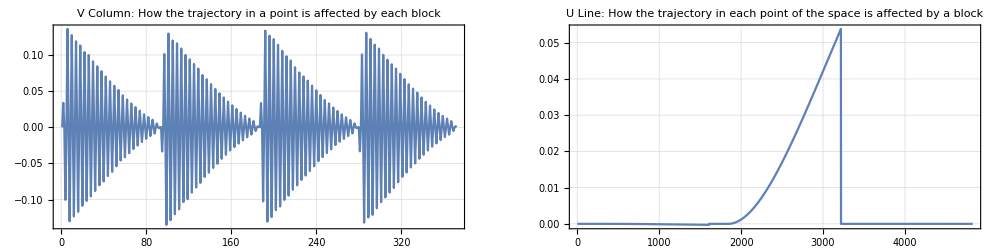

```mathematica
i=1;
GraphicsRow[{ListLinePlot[v[[All,i]],AspectRatio->3/6,PlotTheme->"Detailed",PlotLabel->"V Column: How the trajectory in a point is affected by each block"],
ListLinePlot[u[[All,i]],PlotRange->All,AspectRatio->3/6,PlotTheme->"Detailed",PlotLabel->"U Line: How the trajectory in each point of the space is affected by a block"]},ImageSize->{1000,250}]
```

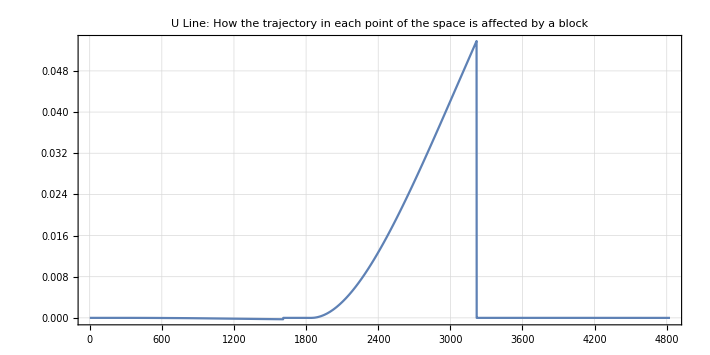

```mathematica
ListLinePlot[ut[[All,1]],PlotRange->All,AspectRatio->3/6,PlotTheme->"Detailed",PlotLabel->"U Line: How the trajectory in each point of the space is affected by a block"]
```

(Sum.b2 1;;i)/(Sum.b2 total) -> “Cov. Percentual”

```mathematica
MinvT=v.winv.ConjugateTranspose[ut];
```

### Ref Type (1): Perfect Undulator

```mathematica
DumpGet[StringJoin[dir,"trajectory1.mx"]];
```

```mathematica
(*Mag*)
mag0=idGenerateMag[typeID,nPeriods,periodL,blockThick,blockGap,symmetry,magnAmp,magError=0];
(*Term*)
term0=idGenerateTerm[termType,blockThick,blockGap,periodL,magnAmp,{{}},{{}},magError=0];
(*Draw*)
device=idDraw[typeID="DeltaUndulator",gap,nPeriods,periodL,blockGeo,blockThick,blockGap,mag0,term0,mode,subdiv ];
(*Solve*)
idSolve[device];
```

```mathematica
(*Field*)
baxis0=idField[device,li,lf,lNpts,{0,0},display=1,oneplot=0];
```

-Graphics-

```mathematica
(*Trajectory*)
trajectory1=idTrajectory[device, eEnergy,r0={0,0,li,0,0,1},lf,lstep,display=0];
```

```mathematica
DumpSave[StringJoin[dir,"trajectory1.mx"],trajectory1];
```

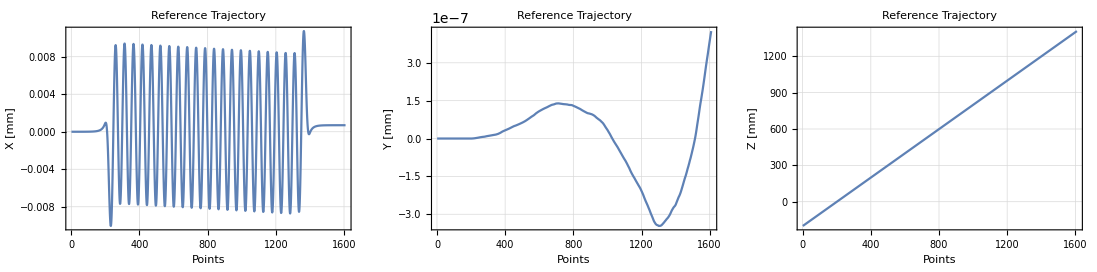

```mathematica
plot=ConstantArray[{},3];
(*Axis Plot*)
plot[[1]]=ListLinePlot[trajectory1[[All,1]],Frame->True,FrameLabel->{"Points",Style["X [mm]",12]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,PlotLabel->"Reference Trajectory"];
plot[[2]]=ListLinePlot[trajectory1[[All,2]],Frame->True,FrameLabel->{"Points",Style["Y [mm]",12]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,PlotLabel->"Reference Trajectory"];
plot[[3]]=ListLinePlot[trajectory1[[All,3]],Frame->True,FrameLabel->{"Points",Style["Z [mm]",12]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,PlotLabel->"Reference Trajectory"];

GraphicsRow[{plot[[1]],plot[[2]],plot[[3]]},Spacings->{0,10},ImageSize->{1200,300},AspectRatio->Full]
```

### Undulator with magnetization errors AND Position errors

```mathematica
device2=idDraw[typeID="DeltaUndulator",gap,nPeriods,periodL,blockGeo,blockThick,blockGap,magnetizations,terminations,mode,subdiv ];
```

```mathematica
nTotalBl=(Length[magnetizations[[1]]]+Length[terminations[[1,1]]]+Length[terminations[[1,4]]])*4;
nCasseteBl=nTotalBl/4;
```

```mathematica
DumpGet[StringJoin[dir,"listShim.mx"]];
listShim=ArrayReshape[listShim,{Length[magnetizations],nCasseteBl}];
(*shimLimit=0.1;
listShim=RandomReal[{-shimLimit,shimLimit},{4,nCasseteBl}];*)
```

```mathematica
(*Apply Shimming*)
For[j=1,j≤Length[magnetizations],j++,
For[i =1,i≤nCasseteBl,i++,
cassetteID=radObjCntStuf[device2][[j]];
radTrfOrnt[radObjCntStuf[cassetteID][[i]],radTrfTrsl[{0,0,listShim[[j,i]]}]];
];
];
```

```mathematica
(*Solve*)
idSolve[device2];
```

```mathematica
(*Show[Graphics3D[radObjDrw[device2],PlotLabel->"Delta Undulator 52.5",BaseStyle->{14,FontFamily->"Times"}],ImageMargins->5,ImageSize->{600,350}]*)
```

```mathematica
(*Trajectory*)
trajectory2=idTrajectory[device2, eEnergy,r0={0,0,li,0,0,1},lf,lstep,display=0];
```

```mathematica
DumpSave[StringJoin[dir,"trajectory2.mx"],trajectory2];
```

```mathematica
(*Field*)
baxis1=idField[device2,li,lf,lNpts,{0,0},display=0,oneplot=0];
```

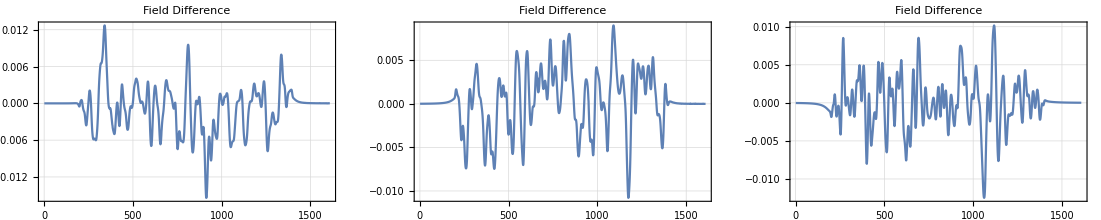

```mathematica
GraphicsRow[{ListLinePlot[baxis1[[All,1]]-baxis0[[All,1]],PlotRange->All,PlotTheme->"Detailed",PlotLabel->"Field Difference"],
ListLinePlot[baxis1[[All,2]]-baxis0[[All,2]],PlotRange->All,PlotTheme->"Detailed",PlotLabel->"Field Difference"],
ListLinePlot[baxis1[[All,3]]-baxis0[[All,3]],PlotRange->All,PlotTheme->"Detailed",PlotLabel->"Field Difference"]},ImageSize->Large]
```

### Trajectory Differences

```mathematica
(*Calculate the Delta_Field needed to correct*)
deltaTraject=Join[trajectory2[[All,1]]-trajectory1[[All,1]],trajectory2[[All,2]]-trajectory1[[All,2]],trajectory2[[All,3]]-trajectory1[[All,3]],1];
```

```mathematica
plot=ConstantArray[{},3];
(*Axis Plot*)
plot[[1]]=ListLinePlot[Table[deltaTraject[[i]],{i,1,Length[deltaTraject]/3}],Frame->True,FrameLabel->{"Points",Style["Trajectory Difference [mm]",12]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,PlotLegends->Placed[{"X"},Above]];
plot[[2]]=ListLinePlot[Table[deltaTraject[[i]],{i,Length[deltaTraject]/3+1,2*Length[deltaTraject]/3}],Frame->True,FrameLabel->{"Points",Style["Trajectory Difference [mm]",12]},PlotTheme->"Detailed",PlotStyle->{Orange},ImageSize->Medium,PlotRange->All,PlotLegends->Placed[{"Y"},Above]];
plot[[3]]=ListLinePlot[Table[deltaTraject[[i]],{i,2*Length[deltaTraject]/3+1,Length[deltaTraject]}],Frame->True,FrameLabel->{"Points",Style["Trajectory Difference [mm]",12]},PlotTheme->"Detailed",PlotStyle->{Green},ImageSize->Medium,PlotRange->All,PlotLegends->Placed[{"Z"},Above]];

GraphicsRow[{plot[[1]],plot[[2]],plot[[3]]},Spacings->{0,10},ImageSize->{1200,300},AspectRatio->Full]
```

-Graphics-

### Calculate Shims

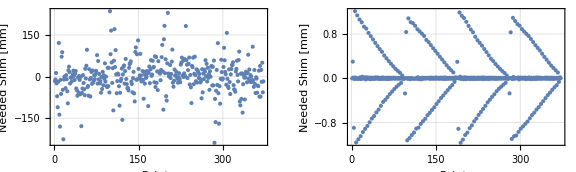

```mathematica
(*Apply the transformation Matrix and Calc the Shimmings*)
shimCalc=Minv.deltaTraject;
shimCalc2=MinvT.deltaTraject;

GraphicsRow[{ListPlot[shimCalc,PlotTheme->"Detailed",FrameLabel->{Style["Points",12],Style["Needed Shim [mm]",12]}],ListPlot[shimCalc2,PlotTheme->"Detailed",FrameLabel->{Style["Points",12],Style["Needed Shim [mm]",12]}]},ImageSize->Large]
```

```mathematica
listShim2=shimCalc2;
```

```mathematica
(*Limit Shimming*)
shimLimit=0.5;

blockIdx=0;
For[j=1,j≤Length[magnetizations],j++,
For[i =1,i≤nCasseteBl,i++,
blockIdx+=1;
If[Abs[listShim2[[blockIdx]]]>shimLimit,
If[listShim2[[blockIdx]]>0,
listShim2[[blockIdx]]=shimLimit;
,
listShim2[[blockIdx]]=-shimLimit];
];
];
];
```

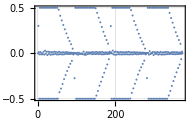

```mathematica
ListPlot[listShim2,PlotTheme->"Detailed",FrameLabel->{Style["Points",12],Style["Real Shim [mm]",12]}]
```

### Corrected Undulator

```mathematica
(*device3=radObjDpl[device2,FreeSym-> False];*)
device3=idDraw[typeID="DeltaUndulator",gap,nPeriods,periodL,blockGeo,blockThick,blockGap,magnetizations,terminations,mode,subdiv ];
(*Apply Shimming*)
For[j=1,j≤Length[magnetizations],j++,
For[i =1,i≤nCasseteBl,i++,
cassetteID=radObjCntStuf[device3][[j]];
radTrfOrnt[radObjCntStuf[cassetteID][[i]],radTrfTrsl[{0,0,listShim[[j,i]]}]];
];
];
```

```mathematica
(*Apply Shimming*)
blockIdx=0;
For[j=1,j≤Length[magnetizations],j++,
For[i =1,i≤nCasseteBl,i++,
blockIdx+=1;
cassetteID=radObjCntStuf[device3][[j]];
radTrfOrnt[radObjCntStuf[cassetteID][[i]],radTrfTrsl[{0,0,listShim2[[blockIdx]]}]];
];
];
```

```mathematica
(*Solve*)
idSolve[device3];
```

```mathematica
(*Trajectory*)
trajectory3=idTrajectory[device3, eEnergy,r0={0,0,li,0,0,1},lf,lstep,display=0];
```

```mathematica
(*Calculate the Delta_Field needed to correct*)
deltaTraject2=Join[trajectory3[[All,1]]-trajectory1[[All,1]],trajectory3[[All,2]]-trajectory1[[All,2]],trajectory3[[All,3]]-trajectory1[[All,3]],1];
```

```mathematica
plot2=ConstantArray[{},3];
(*Axis Plot*)
plot2[[1]]=ListLinePlot[Table[deltaTraject2[[i]],{i,1,Length[deltaTraject2]/3}],Frame->True,FrameLabel->{"Points",Style["Trajectory Difference [mm]",12]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,PlotLegends->Placed[{"X"},Above]];
plot2[[2]]=ListLinePlot[Table[deltaTraject2[[i]],{i,Length[deltaTraject2]/3+1,2*Length[deltaTraject2]/3}],Frame->True,FrameLabel->{"Points",Style["Trajectory Difference [mm]",12]},PlotTheme->"Detailed",PlotStyle->{Orange},ImageSize->Medium,PlotRange->All,PlotLegends->Placed[{"Y"},Above]];
plot2[[3]]=ListLinePlot[Table[deltaTraject2[[i]],{i,2*Length[deltaTraject2]/3+1,Length[deltaTraject2]}],Frame->True,FrameLabel->{"Points",Style["Trajectory Difference [mm]",12]},PlotTheme->"Detailed",PlotStyle->{Green},ImageSize->Medium,PlotRange->All,PlotLegends->Placed[{"Z"},Above]];

GraphicsRow[{plot2[[1]],plot2[[2]],plot2[[3]]},Spacings->{0,10},ImageSize->{1100,300},AspectRatio->Full]
```

-Graphics-

### Shimming Process Results

```mathematica
imsize=Medium;
p11=ListLinePlot[Table[deltaTraject[[i]],{i,1,Length[deltaTraject2]/3}],Frame->True,FrameLabel->{"Points",Style["Field Difference [T]",12]},PlotTheme->"Detailed",PlotRange->All,PlotLegends->Placed[{"Bx_before"},Above],PlotStyle->{Orange,Dashed},ImageSize->imsize];
p12=ListLinePlot[Table[deltaTraject2[[i]],{i,1,Length[deltaTraject2]/3}],Frame->True,FrameLabel->{"Points",Style["Field Difference [T]",12]},PlotTheme->"Detailed",PlotRange->All,PlotLegends->Placed[{"Bx_after"},Above]];

p21=ListLinePlot[Table[deltaTraject[[i]],{i,Length[deltaTraject2]/3+1,2*Length[deltaTraject2]/3}],Frame->True,FrameLabel->{"Points",Style["Field Difference [T]",12]},PlotTheme->"Detailed",PlotRange->All,PlotLegends->Placed[{"By_before"},Above],PlotStyle->{Orange,Dashed},ImageSize->imsize];
p22=ListLinePlot[Table[deltaTraject2[[i]],{i,Length[deltaTraject2]/3+1,2*Length[deltaTraject2]/3}],Frame->True,FrameLabel->{"Points",Style["Field Difference [T]",12]},PlotTheme->"Detailed",PlotRange->All,PlotLegends->Placed[{"By_after"},Above]];

p31=ListLinePlot[Table[deltaTraject[[i]],{i,2*Length[deltaTraject2]/3+1,Length[deltaTraject2]}],Frame->True,FrameLabel->{"Points",Style["Field Difference [T]",12]},PlotTheme->"Detailed",PlotRange->All,PlotLegends->Placed[{"Bz_before"},Above],PlotStyle->{Orange,Dashed},ImageSize->imsize];
p32=ListLinePlot[Table[deltaTraject2[[i]],{i,2*Length[deltaTraject2]/3+1,Length[deltaTraject2]}],Frame->True,FrameLabel->{"Points",Style["Field Difference [T]",12]},PlotTheme->"Detailed",PlotRange->All,PlotLegends->Placed[{"Bz_after"},Above]];

GraphicsRow[{Show[{p11,p12}],Show[{p21,p22}],Show[{p31,p32}]},Spacings->{0,10},ImageSize->{1100,300},AspectRatio->Full]
```

-Graphics-

### Repeat Application

#### Function-Plot Results

```mathematica
plotresults[deltaTraject_,deltaTraject2_]:=(
imsize=Medium;
p11=ListLinePlot[Table[deltaTraject[[i]],{i,1,Length[deltaTraject2]/3}],Frame->True,FrameLabel->{"Points",Style["Trajectory Difference [mm]",12]},PlotTheme->"Detailed",PlotRange->All,PlotLegends->Placed[{"Before"},Above],PlotStyle->{Orange,Dashed},ImageSize->imsize];
p12=ListLinePlot[Table[deltaTraject2[[i]],{i,1,Length[deltaTraject2]/3}],Frame->True,FrameLabel->{"Points",Style["Trajectory Difference [mm]",12]},PlotTheme->"Detailed",PlotRange->All,PlotLegends->Placed[{"After"},Above],ImageSize->imsize];

p21=ListLinePlot[Table[deltaTraject[[i]],{i,Length[deltaTraject2]/3+1,2*Length[deltaTraject2]/3}],Frame->True,FrameLabel->{"Points",Style["Trajectory Difference [mm]",12]},PlotTheme->"Detailed",PlotRange->All,PlotLegends->Placed[{"Before"},Above],PlotStyle->{Orange,Dashed},ImageSize->imsize];
p22=ListLinePlot[Table[deltaTraject2[[i]],{i,Length[deltaTraject2]/3+1,2*Length[deltaTraject2]/3}],Frame->True,FrameLabel->{"Points",Style["Trajectory Difference [mm]",12]},PlotTheme->"Detailed",PlotRange->All,PlotLegends->Placed[{"After"},Above],ImageSize->imsize];

p31=ListLinePlot[Table[deltaTraject[[i]],{i,2*Length[deltaTraject2]/3+1,Length[deltaTraject2]}],Frame->True,FrameLabel->{"Points",Style["Trajectory Difference [mm]",12]},PlotTheme->"Detailed",PlotRange->All,PlotLegends->Placed[{"Before"},Above],PlotStyle->{Orange,Dashed},ImageSize->imsize];
p32=ListLinePlot[Table[deltaTraject2[[i]],{i,2*Length[deltaTraject2]/3+1,Length[deltaTraject2]}],Frame->True,FrameLabel->{"Points",Style["Trajectory Difference [mm]",12]},PlotTheme->"Detailed",PlotRange->All,PlotLegends->Placed[{"After"},Above],ImageSize->imsize];

Print[GraphicsRow[{Show[{p12,p11}],Show[{p22,p21}],Show[{p32,p31}]},Spacings->{0,10},ImageSize->{1100,300},AspectRatio->Full]]
);
```

#### Function-Apply Shim

```mathematica
applyShim[Minv_,deltaTraject_,deltaTraject2_,magnetizations_,nCasseteBl_,device_,eEnergy_,li_,lf_,lstep_,region_]:=(
Module[{device2,listShim3,shimLimit,blockIdx,cassetteID,trajectory4,deltaTraject3},
device2=radObjDpl[device];

(*Calculate Shim*)
listShim3=Minv.deltaTraject2;

(*Limit Shimming*)
shimLimit=0.5;
blockIdx=0;
(*For[j=1,j≤Length[magnetizations],j++,
For[i =1,i≤nCasseteBl,i++,
blockIdx+=1;
If[Abs[listShim3[[blockIdx]]]>shimLimit,
If[listShim3[[blockIdx]]>0,
listShim3[[blockIdx]]=shimLimit;
,
listShim3[[blockIdx]]=-shimLimit];
];
];
];*)
(*Control Region*)
Which[region=="front",
For[i=1*Length[listShim3]/3+1,i≤Length[listShim3],i++, listShim3[[i]]=0];
,region=="middle",
For[i=1,i≤Length[listShim3]/3,i++, listShim3[[i]]=0];
For[i=2*Length[listShim3]/3+1,i≤Length[listShim3],i++, listShim3[[i]]=0];
,region=="exit",
For[i=1,i≤2*Length[listShim3]/3,i++, listShim3[[i]]=0];
];

listShim3=listShim3/Max[Abs[listShim3]]*shimLimit;

(*Apply Shimming*)
blockIdx=0;
For[j=1,j≤Length[magnetizations],j++,
For[i =1,i≤nCasseteBl,i++,
blockIdx+=1;
cassetteID=radObjCntStuf[device2][[j]];
radTrfOrnt[radObjCntStuf[cassetteID][[i]],radTrfTrsl[{0,0,listShim3[[blockIdx]]}]];
];
];
(*Solve*)
idSolve[device2];
(*Trajectory*)
trajectory4=idTrajectory[device2, eEnergy,r0={0,0,li,0,0,1},lf,lstep,display=0];
	(*Calculate the Delta_Field needed to correct*)
deltaTraject3=Join[trajectory4[[All,1]]-trajectory1[[All,1]],trajectory4[[All,2]]-trajectory1[[All,2]],trajectory4[[All,3]]-trajectory1[[All,3]],1];

(*Results*)
plotresults[deltaTraject,deltaTraject3];

Return[{device2,deltaTraject3}]
];
)
```

#### Function-Apply Shim2

```mathematica
applyShim2[Minv_,trajectory1_,deltaTraject_,deltaTraject2_,magnetizations_,nCasseteBl_,device_,eEnergy_,li_,lf_,lstep_]:=(
Module[{device2,listShim3,shimLimit,blockIdx,cassetteID,trajectory4,deltaTraject3},
device2=radObjDpl[device];

(*Calculate Shim*)
listShim3=Minv.deltaTraject2;

(*Limit Shimming*)
shimLimit=0.5;
blockIdx=0;

For[j=1,j≤Length[magnetizations],j++,
For[i =1,i≤nCasseteBl,i++,
blockIdx+=1;
If[Abs[listShim3[[blockIdx]]]>shimLimit,
If[listShim3[[blockIdx]]>0,
listShim3[[blockIdx]]=shimLimit;
,
listShim3[[blockIdx]]=-shimLimit];
];
];
];

(*Apply Shimming*)
blockIdx=0;
For[j=1,j≤Length[magnetizations],j++,
For[i =1,i≤nCasseteBl,i++,
blockIdx+=1;
cassetteID=radObjCntStuf[device2][[j]];
radTrfOrnt[radObjCntStuf[cassetteID][[i]],radTrfTrsl[{0,0,listShim3[[blockIdx]]}]];
];
];
(*Solve*)
idSolve[device2];
(*Trajectory*)
trajectory4=idTrajectory[device2, eEnergy,r0={0,0,li,0,0,1},lf,lstep,display=0];
	(*Calculate the Delta_Field needed to correct*)
deltaTraject3=Join[trajectory4[[All,1]]-trajectory1[[All,1]],trajectory4[[All,2]]-trajectory1[[All,2]],trajectory4[[All,3]]-trajectory1[[All,3]],1];

(*Results*)
plotresults[deltaTraject,deltaTraject3];

Return[{device2,deltaTraject3}]
];
)
```

#### Apply Shim Repeatedly

```mathematica
device4=radObjDpl[device3];
{device4,deltaTraject3}=applyShim[Minv,deltaTraject,deltaTraject2,magnetizations,nCasseteBl,device4,eEnergy,li,lf,lstep,"front"];
```

-Graphics-

```mathematica
out2=applyShim[Minv,deltaTraject,deltaTraject3,magnetizations,nCasseteBl,device4,eEnergy,li,lf,lstep,"middle"];
device4=out2[[1]];deltaTraject3=out2[[2]];
```

-Graphics-

```mathematica
out3=applyShim[Minv,deltaTraject,deltaTraject3,magnetizations,nCasseteBl,device4,eEnergy,li,lf,lstep,"middle"];
device4=out3[[1]];deltaTraject3=out3[[2]];
```

-Graphics-

```mathematica
out4=applyShim[Minv,deltaTraject,deltaTraject3,magnetizations,nCasseteBl,device4,eEnergy,li,lf,lstep,"exit"];
```

-Graphics-

aplicado (1 + 3) vezes a partir do inicial

```mathematica
device4=radObjDpl[device3];
```

```mathematica
{device4,deltaTraject2}=applyShim2[MinvT,trajectory1,deltaTraject,deltaTraject2,magnetizations,nCasseteBl,device4,eEnergy,li,lf,lstep];
```

-Graphics-

#### More Results

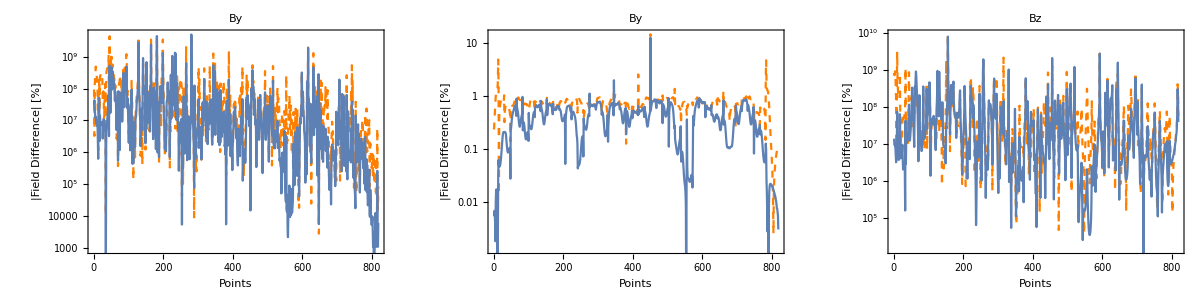

```mathematica
s1=Show[{ListLogPlot[Abs[Table[deltaField[[i]]/baxis0[[i,1]]*100,{i,1,Length[deltaField]/3}]],PlotRange->All,PlotTheme->"Detailed",FrameLabel->{Style["Points",13],Style["|Field Difference| [%]",13]},PlotLabel->Style["By",14,Bold],PlotStyle-> {Orange,Dashed},Joined->True]
,
ListLogPlot[Abs[Table[deltaField2[[i]]/baxis0[[i,1]]*100,{i,1,Length[deltaField]/3}]],PlotRange->All,PlotTheme->"Detailed",Joined->True]}];

s2=Show[{ListLogPlot[Abs[Table[deltaField[[Length[deltaField]/3+i]]/baxis0[[i,2]]*100,{i,1,Length[deltaField]/3}]],PlotRange->All,PlotTheme->"Detailed",FrameLabel->{Style["Points",13],Style["|Field Difference| [%]",13]},PlotLabel->Style["By",14,Bold],PlotStyle-> {Orange,Dashed},Joined->True]
,
ListLogPlot[Abs[Table[deltaField2[[Length[deltaField2]/3+i]]/baxis0[[i,2]]*100,{i,1,Length[deltaField]/3}]],PlotRange->All,PlotTheme->"Detailed",Joined->True]}];

s3=Show[{ListLogPlot[Abs[Table[deltaField[[2*Length[deltaField]/3+i]]/baxis0[[i,3]]*100,{i,1,Length[deltaField]/3}]],PlotRange->All,PlotTheme->"Detailed",FrameLabel->{Style["Points",13],Style["|Field Difference| [%]",13]},PlotLabel->Style["Bz",14,Bold],PlotStyle-> {Orange,Dashed},Joined->True]
,
ListLogPlot[Abs[Table[deltaField2[[2*Length[deltaField2]/3+i]]/baxis0[[i,3]]*100,{i,1,Length[deltaField]/3}]],PlotRange->All,PlotTheme->"Detailed",Joined->True]}];

GraphicsRow[{s1,s2,s3},Spacings->{0,10},ImageSize->{1200,300},AspectRatio->Full]
```

```mathematica
Print["> RMS (By) Difference from Reference Before [%]: ",RootMeanSquare[Table[deltaField[[Length[deltaField]/3+i]]/baxis0[[i,2]]*100,{i,1,Length[deltaField]/3}]]]
```

> RMS (By) Difference from Reference Before [%]: 0.956728

```mathematica
Print["> RMS (By) Difference from Reference After [%]: ",RootMeanSquare[Table[deltaField2[[Length[deltaField2]/3+i]]/baxis0[[i,2]]*100,{i,1,Length[deltaField2]/3}]]]
```

> RMS (By) Difference from Reference After [%]: 0.65529